# Indeterminates, Replace, and Newton

## Dealing with Indeterminates:

If has an optional 4th argument, which lets us choose what should happen if your statement is neither True or False.

```mathematica
IsBig[x_] :=If[x > 2, "Yes is big", "No is not big", "No can tell if big"]
IsBig[3]
```

Yes is big

```mathematica
IsBig[Pi/2]
```

No is not big

```mathematica
IsBig[e]
```

No can tell if big

```mathematica
IsBig[E]
```

Yes is big

```mathematica
IsBig[2]
```

No is not big

## Replace All (/.) as a way of evaluating without setting:

Sometimes we want to evaluate variables without setting them to a value. This can be useful in many settings, we’ll use it to “evaluate” functions in our code without resetting user variables.

```mathematica
powers = Table[x^i, {i, 0, 7}]
```

{1,x,x^2,x^3,x^4,x^5,x^6,x^7}

```mathematica
x = 5;
powers
```

{1,5,25,125,625,3125,15625,78125}

```mathematica
Clear[x];
powers
powers /. x -> 5
```

{1,x,x^2,x^3,x^4,x^5,x^6,x^7}

{1,5,25,125,625,3125,15625,78125}

```mathematica
EvalatFive1[f_] :=f[5];
Clear[f, g, x];
f[x_] = x^2 + 5;
g[x_] = x^3;
EvalatFive1[f]
EvalatFive1[g]
EvalatFive1[x - 5]
```

30

125

(-5+x)[5]

```mathematica
EvalatFive2[f_] :=f/.x->5
EvalatFive2[f[x]]
EvalatFive2[g[x]]
EvalatFive2[x - 5]
```

30

125

0

## Newton Algorithm:

Let’s have a look, and stress test it a bit:

```mathematica
Newton[f_,p_,max_,delta_]:=Module[{p0,p1,Y0,DY0,dp}, (*input function, first guess, # of iterations, and accuracy*)
p0=p; (*Module vars: current estimate, next estimate, y-value, slope, and distance "improved"*)
For[i=0,i<max,i++,
Y0=N[f/.x->p0]; (*Numerical current y-value*)
DY0 = N[D[f,x]/.x->p0];(*Numerical current slope*)
If[DY0==0,Print["Found a horizontal tangent at x =", p0];Return[p0]];
p1= p0-Y0/DY0;(*Compute next iteration*)
dp=Abs[p0-p1];(*Keep track of how much we moved this step*)
 Print["p = ",N[p1],   "\t  |dp| <= ",N[dp],"\t iteration: ",i];
If[dp<delta,Print["Accuracy attained since delta is", delta," and dp is ",dp];Return[p1]];
p0=p1; (*Make new estimate the current estimate and repeat*)
];
Return[p0];
]
```

## First Pass at approximating:

Lets approximate √2 (this should look familiar from Monday):

```mathematica
est = Newton[x^2-2, 4, 10 , .5*10^(-8)]
```

```mathematica
Newton[-2+x^2,4,10,5.*^-9]
```

p = 2.25	  |dp| <= 1.75	 iteration: 0

p = 1.56944	  |dp| <= 0.680556	 iteration: 1

p = 1.42189	  |dp| <= 0.147554	 iteration: 2

p = 1.41423	  |dp| <= 0.00765608	 iteration: 3

p = 1.41421	  |dp| <= 0.0000207234	 iteration: 4

p = 1.41421	  |dp| <= 1.51837×10^-10	 iteration: 5

Accuracy attained since delta is5.×10^-9 and dp is 1.51837×10^-10

1.41421

## Pi to 7 digits

Recall we needed 24 bisections to get this accuracy. Let’s see how Newton does:

```mathematica
Newton[Sin[x], 4, 10, .5*10^(-7)]
```

p = 2.84218	  |dp| <= 1.15782	 iteration: 0

p = 3.15087	  |dp| <= 0.308694	 iteration: 1

p = 3.14159	  |dp| <= 0.00928055	 iteration: 2

p = 3.14159	  |dp| <= 2.66427×10^-7	 iteration: 3

p = 3.14159	  |dp| <= 0.	 iteration: 4

Accuracy attained since delta is5.×10^-8 and dp is 0.

3.14159

## Your Turn!

Exercise 1: Graph f(x)=1-ⅇ^x+x+x^2/2 (use the Plot[] function) and use the code to find the unique zero starting at x_0=10. How much precision do you have after 10 steps? 15? How many steps does it take to get with .1 of the root?

Exercise 2: See how the code handles the function f(x)=-8-8 x+17 x^2-x^3-9 x^4+x^5 starting at x_0=0. Plot the curve, and the tangent lines associated with the cycle.

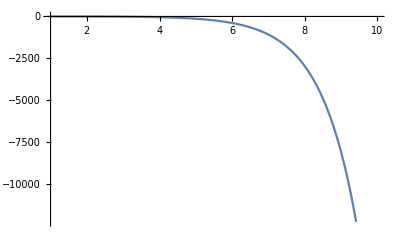

```mathematica
f[x_] = 1 - E^x + x + (x^2/x);
Plot[f[x], {x, 1, 10}]
```